## What is a PDE?

Last week we looked into ordinary differential equations which were equations of single variable functions and their derivatives. This week we’re going to be looking at Partial differential equations or PDEs. And to start off I first want to share a ~18 minute video from the YouTube channel 3B1B which gives a great intuition for what PDEs are. 

As engineers, it tends to be much more important to have  these intuitive understandings of Mathematical concepts, especially when you have tools like Mathematica which can do the nitty-gritty parts of the math for you.

https://www.youtube.com/watch?v=ly4S0oi3Yz8
-Graphics-

## Lets solve our first PDE

### Example form video (With Dirichlet Boundary Conditions)

First we need to know the initial conditions. For this example, let’s try to solve the heat equation starting with the same initial conditions that we saw in the video! 

I’ve gone ahead and ripped the initial conditions from the video and made an interpolating function called IntialConditions, but you could use any function you want for your initial conditions. Once again, I’m just solving the example from the video.

```mathematica
IntialConditions = InterpolatingFunction[…];
```

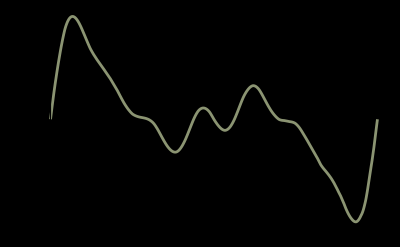

```mathematica
Plot[IntialConditions[x],{x,0,10},ColorFunction->"Rainbow",Background->Black,AxesStyle->White,PlotRangePadding->1]
```

In other words, T(x,t=0) = IntialConditions[x]

Now that we have our initial conditions, we also need our boundary conditions. In the case of the video, we are simulating a rod that is in contact with a 50°C object on both sides. So our initial conditions are as follows: 

T(x=0,t) = 50
T(x=10,t) = 50

And finally, we also need the PDE we’re solving. In this case, we’re solving the heat equation in 1D so: 
(∂T)/(∂t)= α (∂^2 T)/(∂x^2)

Now let’s put all this together in Mathematica using NDSolve. For something like this, it’s pretty simple to the ODE syntax we saw last week

```mathematica
α=0.5;
sol=NDSolve[{
D[T[x,t], t]==α D[T[x,t], x,x],
T[0,t]==50,
T[10,t]==50,
T[x,0]==IntialConditions[x]
},{T},{x,0,10},{t,0,10}][[1]]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{T→InterpolatingFunction[{{0., 10.}, {0., 10.}}, <>]}

And now let’s visualize our solution! 

First by plotting it at discrete time points

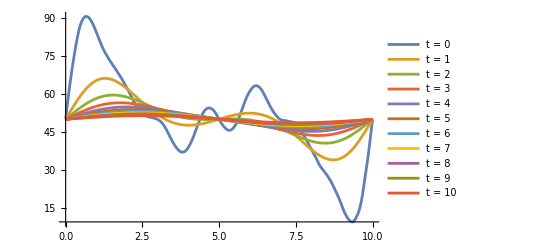

```mathematica
Plot[Evaluate[Table[T[x,t],{t,0,10}]/.sol],{x,0,10},PlotRange->All,PlotLegends->Table["t = "<>ToString[i],{i,0,10}]]
```

And now let’s plot it in 3D

```mathematica
Plot3D[T[x,t]/.sol,{x,0,10},{t,0,10},AxesLabel->{"Position (x)","Time (t)","Temperature (T)"},PlotRange->All,PlotPoints->100]
```

-Graphics3D-

And finally, let’s make some animations!

```mathematica
Animate[Plot[Evaluate[T[x,t]/.sol],{x,0,10},PlotRange->{0,100},ColorFunction->Function[{x},ColorData["Rainbow"][Rescale[T[x,t]/.sol,{9.7,90.4}]]],ColorFunctionScaling->False,Background->Black,AxesStyle->White,PlotRangePadding->1],{t,0,10},AnimationRunning->False]
```

The type of boundary condition we specified (where we fix the value at the end points of the function) is known as a Dirichlet condition. There is actually another way to specify these conditions in Mathematica which yields the same results. This notation uses the DirichletCondition function and the same example is shown below using this syntax:

```mathematica
α=0.5;
sol2=NDSolve[{
D[T[x,t], t]==α D[T[x,t], x,x],
DirichletCondition[T[x,t]==50,True],
T[x,0]==IntialConditions[x]
},{T},{x,0,10},{t,0,10}][[1]]
```

{T→InterpolatingFunction[…]}

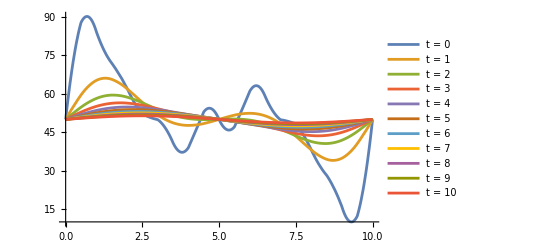

```mathematica
Plot[Evaluate[Table[T[x,t],{t,0,10}]/.sol2],{x,0,10},PlotRange->All,PlotLegends->Table["t = "<>ToString[i],{i,0,10}]]
```

The notation DirichletCondition[T[x, t] == 50, True] means the value of T should be 50 at any boundary points where “True” is true, so in other words at all boundary points (i.e. when x is 0 and 10 in our case). If we instead wanted to make it 40 at the right boundary we could use 2 DirichletCondition lines as follows

```mathematica
α=0.5;
sol3=NDSolve[{
D[T[x,t], t]==α D[T[x,t], x,x],
DirichletCondition[T[x,t]==50,x<5],
DirichletCondition[T[x,t]==40,x>5],
T[x,0]==Piecewise[{{IntialConditions[x], x<10}, {40, x>=10}}]
},{T},{x,0,10},{t,0,10}][[1]]
```

{T→InterpolatingFunction[…]}

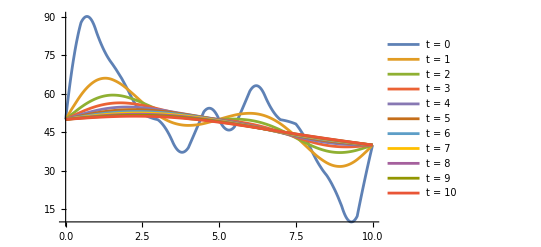

```mathematica
Plot[Evaluate[Table[T[x,t],{t,0,10}]/.sol3],{x,0,10},PlotRange->All,PlotLegends->Table["t = "<>ToString[i],{i,0,10}]]
```

We can see that in this example, the solutions all have T[x=10] = 40. Notice also that we had to change our initial conditions so that they were consistent with the boundary conditions. You never want to have a case where your boundary conditions are inconsistent with your initial conditions. 

There are other ways you can set conditions with DirichletCondition too, but whichever make more sense to you are probably the best unless an error occurs, in which case it could be worth trying to specify your conditions in another way. In this case, we can see we actually get a warning in the first example, but not when we use DirichletCondition. As such, this is the better way to do it for PDEs. Additionally, it is the only way to do it for more complicated examples as we’ll see in a little bit.

### Other Example from video (With Neumann Boundary Conditions)

Another example in the video was modeling the flow of heat between two rods that are brought into contact. Everything about this situation is similar to the previous: We have the distribution at time t=0, we know the heat equation governs the system, but the difference is in the boundary conditions. In this case, the condition is that the derivative of the function with respect to x is zero at both end points. Just like we saw with ODEs last week, we can easily specify functions in terms of derivatives. Let’s use the two rod example to see how. 

First, our initial conditions:

```mathematica
ClearAll[IntialConditions];
IntialConditions[x_]:=Piecewise[{{90, x<=5}, {10, x>5}}]
```

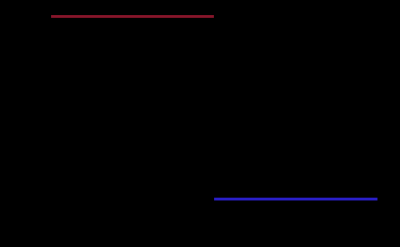

```mathematica
Plot[IntialConditions[x],{x,0,10},Background->Black,ColorFunction->"ThermometerColors",AxesStyle->White]
```

Now lets see what happens over time! Like I said in this case we know that the boundary conditions are as follows: 

(∂T)/(∂x)|_(x=0)= 0
(∂T)/(∂x)|_(x=10)= 0

The reason for these equations is the lack of heat flux through the end of the rods in conjunction with Fourier's law for those who are curious. However understanding heat transfer is not the purpose of this lecture. The key take-away is that in many other classes and areas of engineering you will likely encounter equations like Fourier’s law which will let you derive the boundary conditions from physical assumptions about your system. The point of this lecture is showing you how to use those conditions to get PDE solutions!

Anyway, to specify these conditions, we use similar syntax to DirichletCondition with some small changes as follows using NeumannValue

```mathematica
α=0.5;
sol=NDSolve[{
D[T[x,t], t]-α D[T[x,t], x,x]== NeumannValue[0,True],
T[x,0]==IntialConditions[x]
},{T},{x,0,10},{t,0,100}][[1]];
```

```mathematica
Animate[Plot[T[x,t]/.sol,{x,0,10},Background->Black,ColorFunction->Function[{x},ColorData["ThermometerColors"][Rescale[T[x,t]/.sol,{10,90}]]],ColorFunctionScaling->False,AxesStyle->White,PlotRange->{0,100}],{t,0,100},AnimationRunning->False]
```

Also as a side note, notice the jump in the initial conditions? When you have a discontinuity in a PDE like the heat equation, it will immediately be squashed out in the solution. However this can lead to some error when solving numerically. Instead, it can be beneficial to approximate your initial conditions with a smooth function. 

One way I like to do this is by discretizing the initial conditions, applying a discrete filter like a GaussianFilter, then interpolating to get your function back

InterpolatingFunction[…]

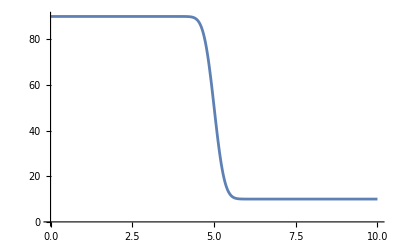

```mathematica
SmoothIC=Interpolation[GaussianFilter[TimeSeries[Table[{x,IntialConditions[x]},{x,0,10,0.01}]],{500,25}]]
Plot[SmoothIC[x],{x,0,10}]
```

```mathematica
α=0.5;
sol2=NDSolve[{
D[T[x,t], t]-α D[T[x,t], x,x]== NeumannValue[0,True],
T[x,0]==SmoothIC[x]
},{T},{x,0,10},{t,0,100}][[1]];
```

```mathematica
Animate[Plot[T[x,t]/.sol2,{x,0,10},Background->Black,ColorFunction->Function[{x},ColorData["ThermometerColors"][Rescale[T[x,t]/.sol,{10,90}]]],ColorFunctionScaling->False,AxesStyle->White,PlotRange->{0,100}],{t,0,100},AnimationRunning->False]
```

This only provides an approximation of the true solution, but it’s good enough for engineering.

NOTE: If you ever don’t specify a boundary Mathematica assumes a Neumann Boundary of 0 at that bound

## Solving PDEs in 2D

Now that we know the basics, let’s solve the heat equation in 2D! 

For instance, let’s say we want to see how the temperature of a evolves over 2D sheet like the one shown around 14:35 in the video. And lets say our initial heat distribution is given by the following function:

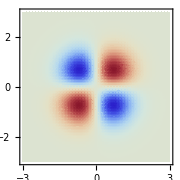
-Graphics--Graphics3D-

```mathematica
InitialCondition[x_,y_]:=(x y)/(ⅇ^(x^2+y^2));
Row[{
DensityPlot[InitialCondition[x,y],{x,-3,3},{y,-3,3},PlotRange->Full,ColorFunction->"ThermometerColors",PlotPoints->100,ImageSize->Small],
Plot3D[InitialCondition[x,y],{x,-3,3},{y,-3,3},PlotRange->Full,ColorFunction->"ThermometerColors",PlotPoints->100,ImageSize->Small,PlotLegends->Automatic]
}]
```

For this PDE lets also say we know our boundary conditions are given such that the temperature along the left boundary is fixed at 0, the derivatives are zero along the top and bottom of the plate, and the right side of the plate is heated with the derivative being equal to 0.01t over time:

T[x=-3,t]  = 0				
∇T = 0 when y = -3 or 3		
∇T = 0.01 t when x = 3

Also can you figure out which condition would be a Dirichlet Condition and which would be a Neumann Condition?

Finally, we also know the PDE we’re solving is the 2D heat equation that we also saw in the video so: 

(∂T)/(∂t) = α ∇^2 T = α((∂^2 T)/(∂x^2)+(∂^2 T)/(∂y^2))

We can type this using either the Nabla notation, or fully type it out ourselves. I prefer to use the Nabla notation because it is more compact and readable

```mathematica
α=0.5;
sol=NDSolve[Evaluate@{
D[T[x,y,t], t]-α ∇_{x,y}^2 T[x,y,t]==NeumannValue[0,y==3∨y==-3]+NeumannValue[0.01t,x==3],
DirichletCondition[T[x,y,t]==0,x==-3],
T[x,y,0]==InitialCondition[x,y]
},T,{x,-3,3},{y,-3,3},{t,0,4}][[1]]
```

{T→InterpolatingFunction[…]}

```mathematica
PrintTemporary["Rendering frame at time:"];
ListAnimate[Monitor[Table[Plot3D[T[x,y,t]/.sol,{x,-3,3},{y,-3,3},PlotRange->{Automatic,Automatic,{-0.2,0.2}},ColorFunction->"ThermometerColors",PlotPoints->100],{t,0,4,0.25}],t],AnimationRunning->False]
```

## 2D PDEs over arbitrary regions

In order to solve PDEs over some region, we first need to know how to make regions in Mathematica! There are a ton of ways to do this, but in general, anything you can make using the Mathematica Graphics function can be made into its own region. You can also make them from images, import them, etc. This is outside the scope of this lecture, but the as always the docs are your friend! 

We’ll make an annular region using Graphics

We will also want to use the NDSolve`FEM` package to solve these more complicated PDEs which we import with:
Needs[“NDSolve`FEM`”]

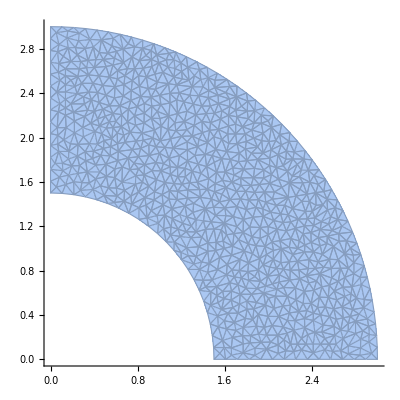

```mathematica
Needs["NDSolve`FEM`"];
reg=Annulus[{0,0},{1.5,3},{0,π/2}];
mesh=DiscretizeRegion[reg,MaxCellMeasure-> 0.005];
Show[mesh,Axes->True]
```

This mesh shows the region we will be solving the PDE over. Mathematica will use all the vertices of this mesh to approximate the spatial derivatives and solve out PDE

Now we need to define our boundary conditions and initial conditions. Lets assume this plate is initially at a temperature of 50, the left side is heated to 100 and the right side is cooled to zero. We will also assume that there is no heat flux across the inner curve but that there is a linearly increasing heat flux across the outer curve. In other words we have: 

IC:
T[x,y,t=0] = 50

BCs:
-Graphics-

We can solve this situation as follows:

```mathematica
α=0.5;
sol=NDSolve[{
D[T[x,y,t], t]-α ∇_{x,y}^2 T[x,y,t]==NeumannValue[2t,x^2+y^2==3^2]+NeumannValue[0,x^2+y^2==1.5^2],
DirichletCondition[T[x,y,t]==0,y==0],
DirichletCondition[T[x,y,t]==100,x==0],
T[x,y,0]==50
},T,{x,y}∈mesh,{t,0,20}][[1]]
```

{T→                                  -17
InterpolatingFunction[{{9.18485 10   , 3.}, {0., 3.}, {0., 20.}}, <>]}

```mathematica
PrintTemporary["Rendering frame at time:"];
ListAnimate[Monitor[Table[DensityPlot[T[x,y,t]/.sol,{x,y}∈reg,ColorFunction->"ThermometerColors",PlotLegends->Automatic],{t,0,20,0.5}],t],AnimationRunning->False]
```

## PDEs in 3D

Finally I want to show you how you can solve PDEs over any 3D mesh. We will be solving the heat equation again, but at steady state for simplicity. In other words we are solving the PDE ∇^2 T=0

```mathematica
Needs["NDSolve`FEM`"];
reg=BoundaryDiscretizeGraphics[ExampleData[{"Geometry3D","SpaceShuttle"}],MaxCellMeasure->0.001]
```

-Graphics3D-

```mathematica
sol=NDSolve[{
Inactive[Laplacian][T[x,y,z],{x,y,z}]==0,
DirichletCondition[T[x,y,z]==0,z>=1∧x>0],
DirichletCondition[T[x,y,z]==1,x<=0]
},T,{x,y,z}∈reg][[1]]
```

{T→InterpolatingFunction[{{-7.64998, 7.04371}, {-4.6821, 4.6821}, {-1.35165, 4.1572}}, <>]}

```mathematica
ElementMeshSurfacePlot3D[T[x,y,z]/.sol,Boxed->False,ViewPoint->{0,-4,2},Axes->True]
```

-Graphics3D-

## Tons of additional great info at: https://reference.wolfram.com/language/tutorial/NDSolveOverview.html